This notebook to test the conjectured relation
D_q^μ = D_q^ψ D_(1+(q-1)D_q^ψ)
between the local spectral dimension D_q^μ, the wavefunction dimension D_q^ψ and the global spectral dimension D_q. All dimensions are averaged over all sites and all wavefunctions.

This relation is verified in the perturbative limit ρ → 0 of the Fibonacci model. It is understood as a consequence of the fact that, in this limit, and for large systems, all but a negligible fraction of the wavefunctions are of the same fractal type.

## Definitions

Fibonacci Hamiltonian.

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
(* Fibo periodic *)
hp[n_,ρ_]:=Block[{F0=Fibonacci[n-2],F1=Fibonacci[n-1],F2=Fibonacci[n],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,1,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]

(* Fibo antiperiodic *)
ha[n_,ρ_]:=Block[{F0=Fibonacci[n-2],F1=Fibonacci[n-1],F2=Fibonacci[n],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,2,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-ρ];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

We consider an infinite system, with a primitive cell consituted of F_n sites (n^th approximant). For this approximant we compute the bandwidths and the intensities of the eigenstates inside a primitive cell.

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBands[n_,ρ_]:=IntBands[n,ρ]=Block[{vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hp[n,ρ]];
{vpa,wfa}=Eigensystem[ha[n,ρ]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

{intensities,bands}]
```

```mathematica
(* averaged q moment of the intensity *)
avqInt[q_,n_,ρ_]:=avqInt[q,n,ρ]=Total[IntBands[n,ρ][[1]]^q,2]/Fibonacci[n];
```

Compute the (averaged) wavefunction dimensions D_q^ψ

```mathematica
(* return a fit function f(x;q,n) = a x + b where a is -Subscript[τ, q]^ψ. nv is a list of approximant sizes used to do the fit *)
linFit[q_,nv_,ρ_]:=Block[{avIntN,data},
avIntN=Map[avqInt[q,#,ρ]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

Compute the (averaged) local spectral dimensions D_q^μ

```mathematica
(* averaged Γ^μ *)
avqInt[τ_,q_,n_,ρ_]:=avqInt[τ,q,n,ρ]=Total[(IntBands[n,ρ][[2]])^-τ Total[IntBands[n,ρ][[1]]^q]]/Fibonacci[n];
```

```mathematica
tauLoc[q_,n_,ρ_]:=τ/.FindRoot[avqInt[τ,q,n-3,ρ]/avqInt[τ,q,n,ρ]-1.,{τ,0.}]
```

Compute the global spectral dimensions D_q

```mathematica
(* Γ *)
Gam[τ_,q_,n_,ρ_]:=Gam[τ,q,n,ρ]=Total[(IntBands[n,ρ][[2]])^-τ Fibonacci[n]^-q];
```

```mathematica
tauSpec[q_,n_,ρ_]:=τ/.FindRoot[Gam[τ,q,n-3,ρ]/Gam[τ,q,n,ρ]-1.,{τ,0.}]
```

## Computations

```mathematica
ρ=.5;
```

### Considerations on the n dependance of the thermodynamic functions χ, Γ and τ.

We see that χ^ψ and Γ^μ exhibit a fluctuation that depends on n (mod 3).

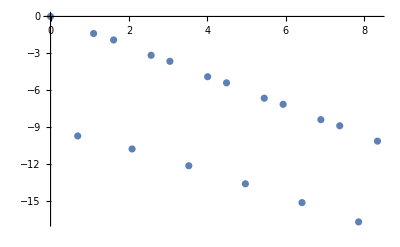

```mathematica
(* χ as a function of n for a given q *)
nValues=Range[2,19,1];
avIntN=Map[avqInt[15.,#,ρ]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

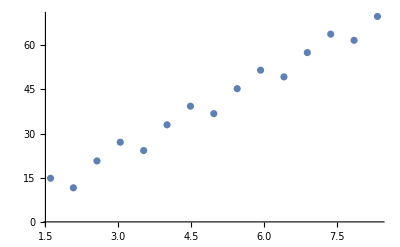

```mathematica
(* Γ as a function of n for given q and τ *)
τ=3.;
nValues=Range[5,19,1];
avIntN=Map[avqInt[τ,10.,#,ρ]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

Because of the 3-periodicity, we compute Γ^n/Γ^(n-3) rather than Γ^n/Γ^(n-1).
The computed value τ_q^n itself depends on n (mod 3).

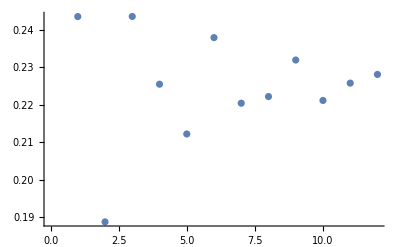

```mathematica
(* τ as a function of n for a given q *)
nValues=Range[8,19,1];
ListPlot[tauLoc[3.,#,ρ]&/@nValues]
```

We see that the function is better converged for n = 0, 2 (mod 3). We will thus chose these value of n in the future.

### Computations

#### D^ψ

We first chose a reasonable range of values for q. We avoid q<0 because on numerical problems (q<0 is sensible to small coefficients, which are not computed accurately).

```mathematica
qValues=Range[0.,0.99,0.05]~Join~Range[1.01,2.,0.1]~Join~Range[2.,20.,0.5]~Join~Range[20.,50.,2.];
```

```mathematica
qValues=Range[0.,15.,0.3];
```

For the computation of χ, we need a range of values of n on which we will do the log-log linear fit. As discussed before, we chose n (mod 3) = 0 or 2, and we also want n to be the largest possible, in what is achievable numerically.
This imposes n = 12, 15, 18.

```mathematica
nValues={13,16,19};
```

```mathematica
(* Compute the fits *)
fits=linFit[#,nValues,ρ]&/@qValues;
```

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqsPsi=-Normal[#["ParameterTable"]][[1,3,2]]&/@fits;
(* convert to Subscript[D, q]^ψ *)
dqsPsi=MapThread[#1/(#2-1)&,{tauqsPsi,qValues}];
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

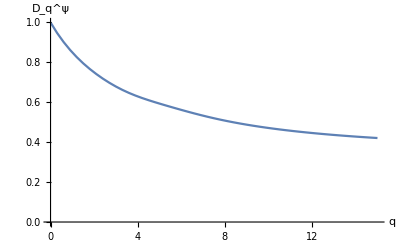

```mathematica
ListPlot[glue[qValues,dqsPsi],Joined->True,AxesLabel->{"q","D_q^ψ"}]
```

#### D^μ

```mathematica
(* n(mod 3) = 0 *)
nValue=19;
τausMu=tauLoc[#,nValue,ρ]&/@qValues;
dqsMu=τausMu/(qValues-1);
```

#### D

We want to check the conjecture
D_q^μ=D_q^ψ D_(1+(q-1)D_q^ψ)
It remains to compute D_q' for q’ in the range 1+(q-1)D_q^ψ, q ∈ qValues.

```mathematica
(* range of values of q over which Subscript[D, q] is computed *)
qVSpec=1+(qValues-1)dqsPsi;
τausSpec=tauSpec[#,nValue,ρ]&/@qVSpec;
dqsSpec=τausSpec/(qVSpec-1);
```

Notice how D_q varies veeeery slowly with q.

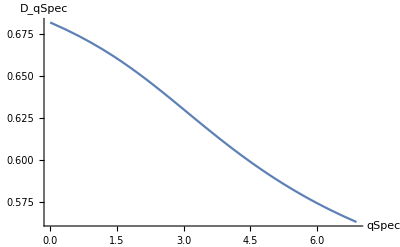

```mathematica
ListPlot[glue[qVSpec,dqsSpec],Joined->True,AxesLabel->{"qSpec","D_qSpec"}]
```

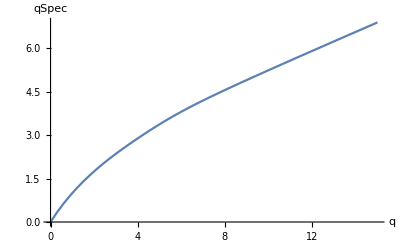

```mathematica
ListPlot[glue[qValues,qVSpec],Joined->True,AxesLabel->{"q","qSpec"}]
```

#### Test relation

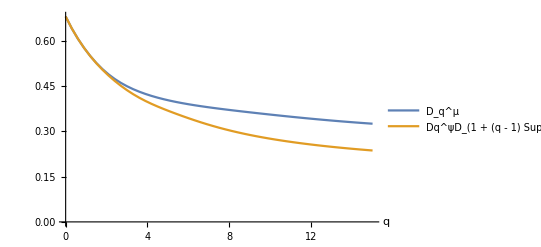

```mathematica
ListPlot[glue[qValues,#]&/@{dqsMu,dqsPsi*dqsSpec},Joined->True,AxesLabel->{"q"},PlotLegends->{"D_q^μ","Dq^ψD_(1 + (q - 1) SuperscriptBox[SubscriptBox[D, q], ψ])"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/relation.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/relation.pdf

```mathematica
lg1=glue[qValues,#]&/@{dqsMu,dqsPsi*dqsSpec};
```

```mathematica
lg09=glue[qValues,#]&/@{dqsMu,dqsPsi*dqsSpec};
```

```mathematica
lg={lg1,lg09};
```

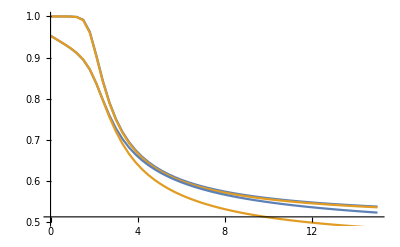

```mathematica
Show[ListPlot[#,Joined->True]&/@{lg1,lg09},PlotRange->{{0,15},{0.5,1.}},AxesLabel->{"q"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/relation_1_09.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/relation_1_09.pdf

When ρ=1, the agreement between theory and numerics is perfect!

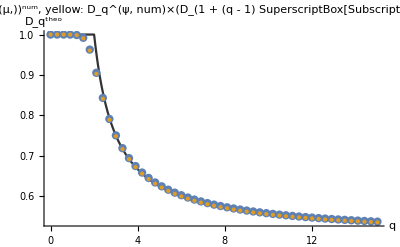

```mathematica
Dth[q_]:=If[q≤2,1,q/(2(q-1))];
(* defalut color scheme *)
{blue,yellow}=ColorData[97,"ColorList"][[1;;2]];
(* point size *)
s=0.015;
(* labels *)
axlbl={"q","D_q^theo"};
pltlbl="blue: (D_q^(μ,))^num, yellow: D_q^(ψ, num)×(D_(1 + (q - 1) SuperscriptBox[SubscriptBox[D, q], ψ]))^num";
Plot[Dth[q],{q,0,15},PlotStyle->{Black,Opacity[0.8]},AxesLabel->axlbl,PlotLabel->pltlbl,Epilog->{{blue,PointSize[s],Point[lg1[[1]]]},{yellow,Point[lg1[[2]]]}}]
```

```mathematica
Export[NotebookDirectory[]<>"data/rel_rho_1.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/rel_rho_1.pdf

When ρ<1, close to 1, the agreement between theory (an article by Sire) and numerics is perfect, except when q ≤ 2. This is imputable to finite-size effects (see the article).

```mathematica
qr=Range[0.,15.,0.3];
testτSpec=tauSpec[#,nValue,ρ]&/@qr;
testdqSpec=testτSpec/(qr-1);
```

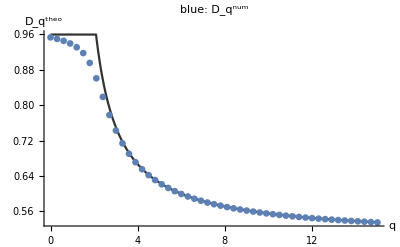

```mathematica
(* theoretical value when ρ -> 1, from an article by Sire *)
Dth[q_,ρ_]:=If[q≤(1-(1-ρ)4 π^-2)/(1-(1-ρ)4 π^-2-1/2),1-(1-ρ)4 π^-2,q/(2(q-1))];
(* point size *)
s=0.012;
(* labels *)
axlbl={"q","D_q^theo"};
pltlbl="blue: D_q^num";
Plot[Dth[q,ρ],{q,0,15},PlotStyle->{Black,Opacity[0.8]},AxesLabel->axlbl,PlotLabel->pltlbl,Epilog->{{blue,PointSize[s],Point[glue[qr,testdqSpec]]}}]
```

```mathematica
Export[NotebookDirectory[]<>"data/comp_theo_num_rho_09.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/comp_theo_num_rho_09.pdf

#### data

This contains the data for ρ=1 and ρ=0.9

```mathematica
(* left and rhs for ρ = 1 *)
```

```mathematica
lg1={{{0.,0.9999999999999115},{0.3,1.0000247718801618},{0.6,1.0000154697372352},{0.8999999999999999,0.9998741032872036},{1.2,0.9988334858625063},{1.5,0.9919571595451584},{1.7999999999999998,0.9627998504420962},{2.1,0.9053532068116951},{2.4,0.8433160704175316},{2.6999999999999997,0.7912023056123343},{3.,0.7504992988581324},{3.3,0.7190241099585908},{3.5999999999999996,0.6943802659499914},{3.9,0.6747027944990719},{4.2,0.6586682692636754},{4.5,0.6453582125239149},{4.8,0.6341309481327345},{5.1,0.6245297938300977},{5.3999999999999995,0.6162224489365565},{5.7,0.6089617589339497},{6.,0.6025601459264095},{6.3,0.5968726450969233},{6.6,0.5917854057496338},{6.8999999999999995,0.5872077252660214},{7.199999999999999,0.5830664160785439},{7.5,0.5793017465363431},{7.8,0.5758644652358067},{8.1,0.5727135852805831},{8.4,0.5698147107616572},{8.7,0.5671387562418423},{9.,0.5646609552278479},{9.299999999999999,0.5623600839814038},{9.6,0.5602178477668929},{9.9,0.558218391025162},{10.2,0.5563479030905901},{10.5,0.5545942982902785},{10.799999999999999,0.5529469544779676},{11.1,0.551396497863194},{11.4,0.5499346248077434},{11.7,0.5485539533585232},{12.,0.5472478988652405},{12.299999999999999,0.5460105692313616},{12.6,0.5448366762664693},{12.9,0.5437214603186631},{13.2,0.5426606259186407},{13.5,0.5416502866006513},{13.799999999999999,0.5406869174076714},{14.1,0.5397673138599349},{14.399999999999999,0.538888556383119},{14.7,0.5380479793670249},{15.,0.537243144166621}},{{0.,0.999999999999913},{0.3,1.0000562450104369},{0.6,0.999993178100345},{0.8999999999999999,0.9997701463802608},{1.2,0.9984870617148409},{1.5,0.990813588888422},{1.7999999999999998,0.9605261870025213},{2.1,0.9029688004373477},{2.4,0.841259051375083},{2.6999999999999997,0.7892723695919297},{3.,0.7484849888852934},{3.3,0.7168275843065076},{3.5999999999999996,0.6919872912181195},{3.9,0.6721389545954752},{4.2,0.6559713202749238},{4.5,0.6425653913830518},{4.8,0.6312745595282494},{5.1,0.6216363700328472},{5.3999999999999995,0.6133131843058633},{5.7,0.6060532901226512},{6.,0.5996653481258178},{6.3,0.5940013427582997},{6.6,0.5889449758580584},{6.8999999999999995,0.5844035973060903},{7.199999999999999,0.5803024805775786},{7.5,0.5765806856285456},{7.8,0.5731880181068788},{8.1,0.5700827600160576},{8.4,0.5672299525629609},{8.7,0.5646000804236678},{9.,0.562168051978694},{9.299999999999999,0.5599124006047207},{9.6,0.5578146530375618},{9.9,0.5558588253888507},{10.2,0.5540310176859892},{10.5,0.5523190851657174},{10.799999999999999,0.5507123698830683},{11.1,0.5492014801031668},{11.4,0.5477781078346704},{11.7,0.5464348770254324},{12.,0.545165216571981},{12.299999999999999,0.5439632535359171},{12.6,0.5428237229127719},{12.9,0.5417418910354128},{13.2,0.540713490267585},{13.5,0.5397346630928982},{13.799999999999999,0.5388019140595666},{14.1,0.5379120683228653},{14.399999999999999,0.5370622357525013},{14.7,0.5362497797527715},{15.,0.5354722900892482}}}
```

```mathematica
(* left and rhs for ρ = 0.9 *)
```

```mathematica
lg09={{{0.,0.9530903224285642},{0.3,0.9434853452795122},{0.6,0.9337892158028431},{0.8999999999999999,0.9233207475484935},{1.2,0.9109669753676418},{1.5,0.894776516406977},{1.7999999999999998,0.8710242178363268},{2.1,0.8368343929774658},{2.4,0.7969493282595392},{2.6999999999999997,0.7593420498833245},{3.,0.727671588833518},{3.3,0.7019962383991709},{3.5999999999999996,0.6811962364987295},{3.9,0.6641084167721824},{4.2,0.6498216850910726},{4.5,0.6376771245769773},{4.8,0.6272046182011348},{5.1,0.6180645688363271},{5.3999999999999995,0.6100063482035891},{5.7,0.6028406820157561},{6.,0.5964215113156234},{6.3,0.5906339414536539},{6.6,0.5853860706135844},{6.8999999999999995,0.5806033198201439},{7.199999999999999,0.5762244078046631},{7.5,0.5721984316668483},{7.8,0.5684827076253608},{8.1,0.5650411454072062},{8.4,0.5618430047459482},{8.7,0.5588619304877008},{9.,0.5560751942281121},{9.299999999999999,0.5534630913737775},{9.6,0.5510084567806538},{9.9,0.5486962719905566},{10.2,0.5465133440304875},{10.5,0.5444480407011991},{10.799999999999999,0.5424900708779226},{11.1,0.5406303009882256},{11.4,0.5388606007968462},{11.7,0.5371737131055017},{12.,0.5355631430993834},{12.299999999999999,0.5340230639348366},{12.6,0.5325482358310936},{12.9,0.5311339364511127},{13.2,0.5297759007677523},{13.5,0.5284702689375964},{13.799999999999999,0.527213540965157},{14.1,0.5260025371494366},{14.399999999999999,0.5248343634739904},{14.7,0.5237063812391604},{15.,0.5226161803475209}},{{0.,0.9530903224285644},{0.3,0.9435863035243692},{0.6,0.9338962830283719},{0.8999999999999999,0.9234572404498741},{1.2,0.9111590192819933},{1.5,0.8950365632762215},{1.7999999999999998,0.8713675827822565},{2.1,0.8370406133240369},{2.4,0.7958664657780737},{2.6999999999999997,0.7554058929623253},{3.,0.7198961345555208},{3.3,0.6901536804994587},{3.5999999999999996,0.6655582802697211},{3.9,0.6451604500416249},{4.2,0.6280812126858297},{4.5,0.6136105352805226},{4.8,0.6012023935031898},{5.1,0.5904431667641905},{5.3999999999999995,0.5810193288669131},{5.7,0.5726913005635985},{6.,0.5652739180319905},{6.3,0.5586222651576435},{6.6,0.5526214709512575},{6.8999999999999995,0.5471793388461275},{7.199999999999999,0.5422209785613941},{7.5,0.5376848565902879},{7.8,0.5335198591650255},{8.1,0.5296830851462444},{8.4,0.5261381709944312},{8.7,0.5228540079599702},{9.,0.5198037515124951},{9.299999999999999,0.5169640506948994},{9.6,0.5143144444674417},{9.9,0.5118368858329017},{10.2,0.5095153643681979},{10.5,0.5073356049214548},{10.799999999999999,0.5052848254763145},{11.1,0.503351541090549},{11.4,0.5015254037651248},{11.7,0.49979707035670407},{12.,0.49815809239324116},{12.299999999999999,0.49660082301794684},{12.6,0.4951183373607245},{12.9,0.49370436348367314},{13.2,0.4923532217155332},{13.5,0.4910597707146146},{13.799999999999999,0.4898193590088638},{14.1,0.4886277810771324},{14.399999999999999,0.4874812372758535},{14.7,0.4863762970950485},{15.,0.4853098653598624}}}
```